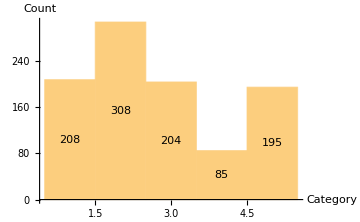

```mathematica
weights={200,300,200,100,200};
categories=Range[1,Length[weights]];
dist=EmpiricalDistribution[weights->categories];
data=RandomVariate[dist,1000];
Histogram[data,LabelingFunction-> Center,AxesLabel->{"Category","Count"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/sampling_from_discrete_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\sampling_from_discrete_distribution.pdf

```mathematica
doorsWithPrize=RandomChoice[{1,2,3},1000];
firstChoice=RandomChoice[{1,2,3},Length[doorsWithPrize]];
doorsWithoutPrize=MapThread[RandomChoice[Complement[{1,2,3},{#1,#2}]]&,{doorsWithPrize,firstChoice}];
secondChoice=MapThread[RandomChoice[Complement[{1,2,3},{#1,#2}]]&,{doorsWithoutPrize,firstChoice}];
ProbabilityWinningPrize[choice_]:=Apply[Plus,MapThread[Boole[#1==#2]&,{doorsWithPrize,choice}]]/Length[doorsWithPrize]//N;
Print["Probability of winning by staying with your first choice = ",ProbabilityWinningPrize[firstChoice]];
Print["Probability of winning by choosing the remaining door = ",ProbabilityWinningPrize[secondChoice]];
```

Probability of winning by staying with your first choice = 0.333221

Probability of winning by choosing the remaining door = 0.666779

```mathematica
dist=TransformedDistribution[x^2,x\[Distributed]NormalDistribution[0,σ]];
PDF[dist,y]
```

Piecewise[{{(ⅇ^(-y/(2 σ^2)))/(√(2 π) √y σ), y>0}, {0, y<0}, {Indeterminate, True}}]

```mathematica
TransformedDistribution[u+v,{u\[Distributed]PoissonDistribution[λ1],v\[Distributed]PoissonDistribution[λ2]}]
```

PoissonDistribution[λ1+λ2]

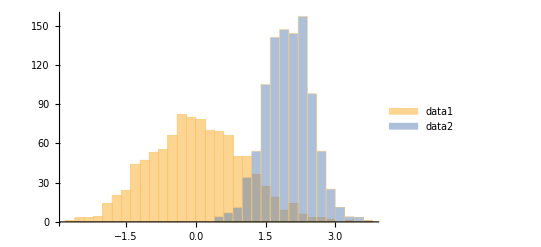

```mathematica
data1=RandomVariate[NormalDistribution[0,1], 1000];
data2=RandomVariate[NormalDistribution[2,0.5], 1000];
Histogram[{data1,data2}, ChartLegends->{"data1","data2"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/normal_distributions_from_data.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\normal_distributions_from_data.pdf

```mathematica
Histogram3D[RandomVariate[BinormalDistribution[0],10000]]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/histogram_3d.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\histogram_3d.pdf

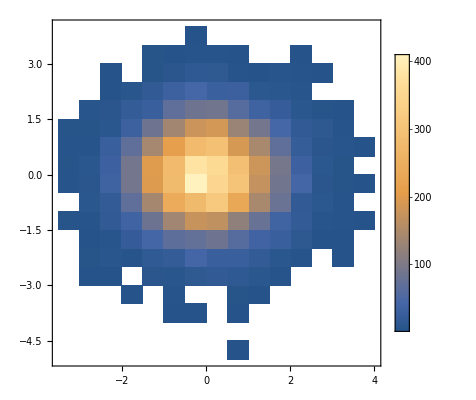

```mathematica
DensityHistogram[RandomVariate[BinormalDistribution[0],10000], ChartLegends->Automatic]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/density_histogram.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\density_histogram.pdf

```mathematica
dist=ProbabilityDistribution[Sqrt[2]/Pi/α/(1+(x/α)^4),{x,-Infinity,Infinity}, Assumptions->{α>0}];
(* dist=ProbabilityDistribution[1/(1+x^4),{x,-Infinity,Infinity},Method->"Normalize"];*)
```

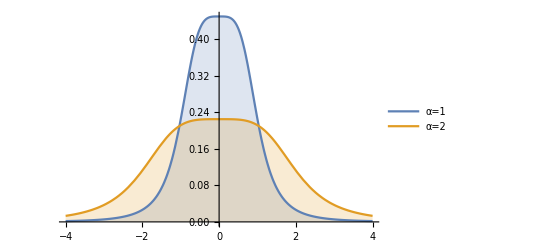

```mathematica
Plot[{PDF[dist,x]//.{α->1},
PDF[dist,x]//.{α->2}},{x,-4,4},Filling->Axis, PlotLegends->Placed[{"α=1","α=2"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/probability_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\probability_distribution.pdf

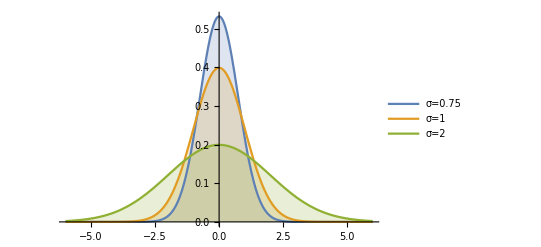

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis,PlotLegends->Placed[{"σ=0.75","σ=1","σ=2"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/normal_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\normal_distribution.pdf

```mathematica
Plot3D[PDF[MultinormalDistribution[{0,0},{{2,1},{1,2}}],{x,y}],{x,-4,4},{y,-4,4}, PlotPoints->{50,50}]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/multi_normal_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\multi_normal_distribution.pdf

```mathematica
dist=ProbabilityDistribution[Gamma[3/4]/(Gamma[5/4]*Sqrt[2 Pi^3])/(1+x^4+y^4),{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
```

```mathematica
Plot3D[PDF[dist,{x,y}],{x,-4,4},{y,-4,4},PlotRange->{0,0.2},PlotPoints->{50,50}]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/joint_probability_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\joint_probability_distribution.pdf

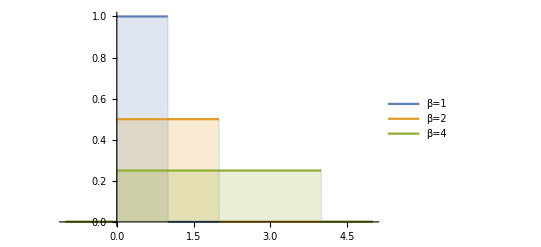

```mathematica
Plot[Table[PDF[UniformDistribution[{0, β}],x],{β,{1,2,4}}]//Evaluate,{x,-1,5},Filling->Axis,PlotRange-> {0,1},PlotLegends->Placed[{"β=1","β=2","β=4"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/uniform_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\uniform_distribution.pdf